# WikiMap: Dynamic Classifier

Tetyana Loskutova
Wolfram Summer School 2017
tetyana.loskutova@gmail.com

## Outline

#### Classifying text that has not been written yet

#### How to use recurrent nets?

#### An application: integer addition

#### Advanced application: question answering

## The problem

Try predict the next character in the sequence:

{W, h, y, “ “, a, r, e, “ “ , y, o, u, “ “, a, s, k, i, n}

The prediction method must have a notion of order: the exact order of the sequence matters!

Ordinary neural nets don’t have any notion of order.

Solution: recurrent networks! (or RNN’s)

## Why recurrent nets are interesting

### Lots of Applications

Speech Recognition

All state-of-the-art speech recognition systems make use of RNN’s

e.g Baidu’s Deep Speech 2

https://arxiv.org/abs/1512.02595

Speech Synthesis

Tacotron: Towards End-to-End Speech Synthesis, Wang et al.

https://arxiv.org/abs/1703.10135

Cool demo: https://google.github.io/tacotron/

Language Translation

Google Translate switched to using RNN’s last year (their system: https://arxiv.org/abs/1609.08144)

“As dawn broke over Tokyo, Google Translate was the No. 1 trend on Japanese Twitter, just above some cult anime series and the long-awaited new single from a girl-idol supergroup. Everybody wondered: How had Google Translate become so uncannily artful?”, see https://www.nytimes.com/2016/12/14/magazine/the-great-ai-awakening.html

## Why recurrent nets are interesting

### Lots of Applications

Image Caption Generation

Taken from: http://googleresearch.blogspot.com/2014/11/a-picture-is-worth-thousand-coherent.html

## Why recurrent nets are interesting

### Lots of Applications

Question Answering

An example from the Squad Dataset (https://rajpurkar.github.io/SQuAD-explorer/):

Context:

One of the most famous people born in Warsaw was Maria Skłodowska-Curie, who achieved international recognition for her research on radioactivity and was the first female recipient of the Nobel Prize. Famous musicians include Władysław Szpilman and Frédéric Chopin. Though Chopin was born in the village of Żelazowa Wola, about 60 km (37 mi) from Warsaw, he moved to the city with his family when he was seven months old. Casimir Pulaski, a Polish general and hero of the American Revolutionary War, was born here in 1745.

Question:

What was Maria Curie the first female recipient of?

Prediction by Match-LSTM network:

Nobel Prize

Others

sentiment analysis

language modelling

time series prediction

## Why recurrent nets are interesting

### They are arbitrarily powerful models

Theorem (Universal Approximation Theorem): NetChain[{DotPlusLayer[n], ElementwiseLayer[Tanh]}] can approximate any continuous function (on a compact subset of R^n) arbitrary well for some finite number of neurons n.

Theorem: Recurrent neural networks are Turing Complete (Siegelmann, H. T. and Sontag, E. D. (1995))

## What is a recurrent network

Recurrent neural nets have feedback loops:

A feedback loop can be “unrolled”:

This is now a feedforward network with parameter sharing:

Taken from: http://colah.github.io/posts/2015-08-Understanding-LSTMs/

## What is a recurrent network

RNN’s are very simple to implement:

```mathematica
rnnTimeStep[params_Association,input_,state_]:=Tanh[params["StateWeights"].state+params["InputWeights"].input+params["Biases"]];
```

```mathematica
rnnLayerForward[params_Association,input_,state_]:=Rest@FoldList[rnnTimeStep[params,#2,#1]&,state,input]
```

Find the derivative function is harder though.

A nice blog post exploring the link between functional programming and neural nets:

http://colah.github.io/posts/2015-09-NN-Types-FP/

## What is a recurrent network

Lets show that this is the same as BasicRecurrentLayer:

```mathematica
sequenceLength=3;
featureSize=2;
rnnStateSize=1;
inData=RandomReal[1,{sequenceLength,featureSize}];
state=ConstantArray[0,rnnStateSize];
```

Create a BasicRecurrentLayer and initialize it:

```mathematica
net=NetInitialize@BasicRecurrentLayer[rnnStateSize,"Input"->Dimensions@inData]
```

BasicRecurrentLayer[<>]

Extract its parameters:

```mathematica
param=NetExtract[net,"Arrays"]
```

<|InputWeights→{{-0.529935,-0.423679}},StateWeights→{{-1.61389}},Biases→{0.}|>

Evaluate the built-in Mathematica implementation:

```mathematica
net[inData]
```

{{-0.232319},{0.286184},{-0.582591}}

Evaluate our own implementation:

```mathematica
rnnLayerForward[param,inData,state]
```

{{-0.232319},{0.286184},{-0.582591}}

## What is a recurrent network

### What about LSTM’s, GRU’s, etc?

Plain RNN’s have traditionally been hard to train

RNN == very deep feedforward network!

Exploding/vanishing gradients

```mathematica
<<NeuralNetworks`
```

NetChain[]

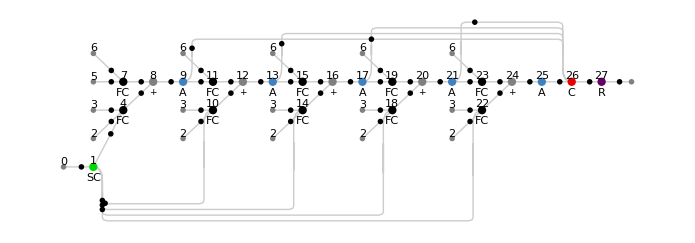

```mathematica
net=NetChain[{BasicRecurrentLayer[4]},"Input"->{"Varying",5}]
sequenceLen=5;
MXPlanPlot[net,sequenceLen]
```

#### For More:

Exploding/vanishing gradients problem was discovered by Sepp Hochreiter and described in his 1991 diploma thesis (Untersuchungen zu dynamischen neuronalen Netzen. Diploma thesis, TU Munich, 1991, http://people.idsia.ch/~juergen/SeppHochreiter1991ThesisAdvisorSchmidhuber.pdf)

On the difficulty of training recurrent neural networks, Pascanu et al, http://proceedings.mlr.press/v28/pascanu13.pdf

## What is a recurrent network

### What about LSTM’s, GRU’s, etc?

More complicated RNN’s have been proposed to allow for simpler training.

Consider a BasicRecurrentLayer:

Now consider a LongShortTermMemoryLayer:

Taken from: http://colah.github.io/posts/2015-08-Understanding-LSTMs/

Lots of variants (LSTM, GRU):

Define your own using NetFoldOperator!

## Example: Integer Addition

Generate training data:

```mathematica
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->a+b;
trainingData=Flatten@Table[makeRule[i,j],{i,0,99},{j,0,99}];
RandomSample[trainingData,4]//InputForm
```

{"97+60" -> 157, "37+89" -> 126, "19+56" -> 75, 
 "27+29" -> 56}

```mathematica
"97+60"
```

Define a NetEncoder:

```mathematica
enc=NetEncoder[{"Characters",{DigitCharacter,"+"}}];
```

```mathematica
enc@"97+60+"
```

{10,8,11,7,1,11}

Define a net that takes a sequence of character inputs and predicts a number:

```mathematica
net=NetChain[{UnitVectorLayer[],LongShortTermMemoryLayer[40],LongShortTermMemoryLayer[20],SequenceLastLayer[],LinearLayer[]},"Input"->enc,"Output"->"Real"]
```

NetChain[]

## Example: Integer Addition (continued)

Train the net:

```mathematica
trained=NetTrain[net,trainingData,BatchSize->64,MaxTrainingRounds->200,ValidationSet->Scaled[0.1]]
```

NetChain[]

Evaluate on some examples:

```mathematica
trained[{"5+2","10+25","9+11","44+44"}]
```

{6.47626,35.1461,20.7937,88.0641}

## Example: Question Answering

Get the data:

```mathematica
ro=ResourceObject["The 20-Task bAbI Question-Answering Dataset v1.2"]
```

ResourceObject[…]

```mathematica
traindata=ResourceData[ro,"TrainingData"]["Task1"];
testdata=ResourceData[ro,"TestData"]["Task1"];
```

```mathematica
traindata[[All,100]]
```

<|Context→Mary went back to the bedroom. Mary travelled to the bathroom. John travelled to the office. Mary travelled to the bedroom. John journeyed to the kitchen. John moved to the hallway. Daniel moved to the hallway. Mary went back to the garden. Daniel went back to the office. Daniel travelled to the kitchen.,Question→Where is Daniel?,Answer→kitchen|>

## Example: Question Answering (continued)

Get all the words used:

```mathematica
dict=Union@@TextWords[Join[traindata["Context"],traindata["Question"]]]
```

{back,bathroom,bedroom,Daniel,garden,hallway,is,John,journeyed,kitchen,Mary,moved,office,Sandra,the,to,travelled,went,Where}

Get all the classes predicted:

```mathematica
classes=Union[traindata["Answer"]]
```

{bathroom,bedroom,garden,hallway,kitchen,office}

Create a NetEncoder for words:

```mathematica
enc=NetEncoder[{"Tokens",Join[dict,{"."}]}]
```

NetEncoder[<>]

## Example: Question Answering (continued)

Define a network taking a question, a context, and which predicts an answer:

```mathematica
net=NetGraph[<|
"context"->{EmbeddingLayer[50],DropoutLayer[0.3]},"question"->{EmbeddingLayer[50],DropoutLayer[0.3],LongShortTermMemoryLayer[50],SequenceLastLayer[]},
"cat"->CatenateLayer[],
"classifier"->{LongShortTermMemoryLayer[50],SequenceLastLayer[],DropoutLayer[0.3],LinearLayer[Length[classes]],SoftmaxLayer[]}|>,
{NetPort["Context"]->"context",NetPort["Question"]->"question",
{"question","context"}->"cat","cat"->"classifier"->NetPort["Answer"]},
"Context"->enc,"Question"->enc,"Answer"->NetDecoder[{"Class",classes}]]
```

NetGraph[]

## Example: Question Answering (continued)

Train the net:

```mathematica
trainedNet=NetTrain[net,traindata,ValidationSet->testdata,MaxTrainingRounds->15]
```

NetGraph[]

```mathematica
trainedNet[<|"Context"->"Sandra went to the office. Sandra travelled to the bathroom. Mary went back to the bedroom. Daniel moved to the garden. John journeyed to the garden. Daniel went back to the hallway. John journeyed to the bedroom. Mary travelled to the kitchen. Sandra went to the bedroom. Daniel went to the garden.","Question"->"Where is Daniel?"|>]
```

garden

Obtain the accuracy of the trained net on the test set:

```mathematica
N@Count[trainedNet[KeyDrop[testdata,"Answer"]]-testdata["Answer"],0]/Length[testdata["Answer"]]
```

0.527

## Sequence-to-Sequence

Translating between two languages

Speech recognition, etc

### Integer Addition: Part 1

Special case: output sequence of fixed length

```mathematica
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->IntegerString[a+b];
data=RandomSample[Flatten@Table[makeRule[i,j],{i,0,999},{j,0,999}],40000];
data[[;;,2]]=StringPadRight[data[[;;,2]],4];
{testData,trainingData}=TakeDrop[data,Ceiling[Length[data]/10]];
```

```mathematica
RandomSample[trainingData,4]
```

{245+507→752 ,616+383→999 ,320+91→411 ,235+222→457 }

### Integer Addition: Part 1

https://arxiv.org/pdf/1409.3215.pdf

### Integer Addition: Part 1

```mathematica
encoder=NetChain[{UnitVectorLayer[11],
LongShortTermMemoryLayer[128],
SequenceLastLayer[]}]
```

NetChain[]

```mathematica
decoder=NetChain[{ReplicateLayer[4],
LongShortTermMemoryLayer[128],
NetMapOperator[LinearLayer[]],
SoftmaxLayer[]}]
```

NetChain[]

```mathematica
net=NetChain[{encoder,decoder},
"Input"->NetEncoder[{"Characters",{DigitCharacter,"+"}}],
"Output"->NetDecoder[{"Characters",{DigitCharacter," "}}]]
```

NetChain[]

### Integer Addition: Part 1

```mathematica
trainedNet=NetTrain[net,trainingData,ValidationSet->testData,MaxTrainingRounds->40]
```

NetChain[]

```mathematica
StringTrim@trainedNet[{"2+432","100+43","400+500"}]
```

{33,446,811}

## Detour: Attention

For Seq2Seq, input sequence is usually represented by a single vector

A single vector representing a long sequence can be a bottleneck

https://arxiv.org/pdf/1409.3215.pdf

## Detour: Attention

One solution: Attention

Bahdanau et al, https://arxiv.org/pdf/1409.0473.pdf

http://distill.pub/2016/augmented-rnns

## Detour: Attention

```mathematica
attend=NetInitialize@SequenceAttentionLayer["Input"->{"Varying",2},"Query"->{"Varying",1}]
```

SequenceAttentionLayer[<>]

```mathematica
attend[<|"Input"->{{1,2},{3,4}},"Query"->{{5},{6},{7},{8}}|>]//MatrixForm
```

(2.97161 | 3.97161
2.98775 | 3.98775
2.99473 | 3.99473
2.99774 | 3.99774)

```mathematica
NetExtract[seq,"ScoringNet"]
```

NetGraph[]

Very simple to define in WL

```mathematica
attentionFunction[input_,query_,scorer_]:=Map[Function[q,Mean@WeightedData[input,Exp[scorer[<|"Input"->#,"Query"->q|>]]&]],query];
```

## Attention Example: Sorting

```mathematica
digits=Range[6];
seqs=RandomSample[Flatten[Table[Tuples[digits,n],{n,3,6}],1]];
data=Map[#->Sort[#]&,seqs];
{testData,trainData}=TakeDrop[data,Ceiling[Length[data]/10]];
```

```mathematica
RandomSample[trainData,3]
```

{{1,5,1,1,1,3}→{1,1,1,1,3,5},{4,1,6,6,5,6}→{1,4,5,6,6,6},{4,4,5,6,2,6}→{2,4,4,5,6,6}}

```mathematica
net = NetGraph[<|
"enc"->{EmbeddingLayer[12],LongShortTermMemoryLayer[50]},"dec"->LongShortTermMemoryLayer[50],"attend"->SequenceAttentionLayer[],
"cat"->CatenateLayer[2],"classify"->{NetMapOperator[LinearLayer[]],SoftmaxLayer[]}
|>,{
"enc"->"dec"->NetPort["attend","Query"],"enc"->NetPort["attend","Input"],
"dec"->"cat","attend"->"cat","cat"->"classify"},"Input"->{"Varying",NetEncoder[{"Class",digits}]},"Output"->{"Varying",NetDecoder[{"Class",digits}]}
]
```

NetGraph[]

## Attention Example: Sorting

```mathematica
trained=NetTrain[net,trainData,MaxTrainingRounds->3,ValidationSet->testData]
```

NetGraph[]

```mathematica
trained[{6,6,1,4,2}]
```

{1,1,4,6,6}

## Advanced: General Integer Addition with Attention

Now lets solve the general seq2seq problem

Variable-length input AND variable length output

## Advanced: General Integer Addition with Attention

```mathematica
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->IntegerString[a+b];
data=RandomSample[Flatten@Table[makeRule[i,j],{i,0,999},{j,0,999}],60000];
{testData,trainingData}=TakeDrop[data,Ceiling[Length[data]/10]];
```

```mathematica
RandomSample[trainingData,4]
```

{737+367→1104,512+297→809,27+848→875,954+768→1722}

Create a NetEncoder that uses a special code for the start and end of a string, which will be used to indicate the beginning and end of the output sequence:

```mathematica
targetEnc=NetEncoder[{"Characters",{DigitCharacter,{StartOfString,EndOfString}->Automatic}}]
```

NetEncoder[<>]

Create a similar encoder for the input, which contains a "+":

```mathematica
inputEnc=NetEncoder[{"Characters",{DigitCharacter,"+"}}]
```

NetEncoder[<>]

## Advanced: General Integer Addition with Attention

Define a net that takes a sequence of inputs and returns a single vector of size 150 as output:

```mathematica
encoderNet=NetChain[{UnitVectorLayer[],GatedRecurrentLayer[150],SequenceLastLayer[]}]
```

NetChain[]

```mathematica
decoderNet=NetGraph[{
UnitVectorLayer[11],
SequenceMostLayer[],
GatedRecurrentLayer[150]},
{NetPort["Input"]->1->2->3,
NetPort["State"]->NetPort[3,"State"]}
]
```

NetGraph[]

## Advanced: General Integer Addition with Attention

Define training net ready for teacher-forcing:

```mathematica
trainingNet=NetGraph[<|
"encoder"->encoderNet,
"decoder"->decoderNet,
"classifier"->{NetMapOperator[LinearLayer[]],
SoftmaxLayer[]},
"loss"->CrossEntropyLossLayer["Index"],
"rest"->SequenceRestLayer[]|>,
{NetPort["Input"]->"encoder"->NetPort["decoder","State"],
NetPort["Target"]->NetPort["decoder","Input"],
"decoder"->"classifier"->NetPort["loss","Input"],
NetPort["Target"]->"rest"->NetPort["loss","Target"]},
"Input"->inputEnc,"Target"->targetEnc]
```

NetGraph[]

## Advanced: General Integer Addition with Attention

Train the net:

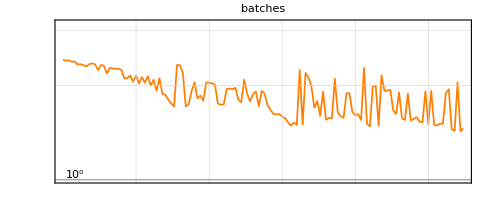
{NetGraph[],-Graphics-}

```mathematica
{trainedNet,lossPlot}=NetTrain[trainingNet,trainingData,Automatic,{"TrainedNet","LossEvolutionPlot"},ValidationSet->testData,MaxTrainingRounds->30]
```

## Advanced: General Integer Addition with Attention

### Generation

Plot the loss for all possible outputs:

```mathematica
lossPlot[net_,input_]:=ListPlot[net[<|"Input"->ConstantArray[input,1999],"Target"->Table[ToString[i],{i,1999}]|>],AxesLabel->{"sum","loss"}];
```

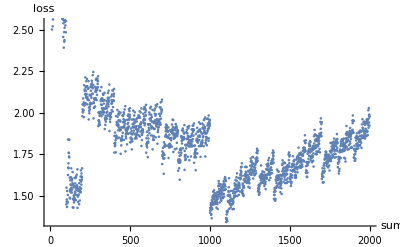

```mathematica
lossPlot[trainedNet,"200+300"]
```

Predict by finding the minimum loss:

```mathematica
predict[net_,input_]:=First@Ordering[net[<|"Input"->ConstantArray[input,1999],"Target"->Table[ToString[i],{i,1999}]|>],1]-1
```

```mathematica
predict[trainedNet,#]&/@{"34+200","32+87","344+77"}
```

{103,103,1099}

## Advanced: General Integer Addition with Attention

### Generation

Prediction approach: explicit generation

```mathematica
trainedEncoder=NetReplacePart[NetExtract[trainedNet,"encoder"],"Input"->inputEnc]
trainedDecoder=NetExtract[trainedNet,"decoder"]
```

NetChain[]

NetGraph[]

Use a SequenceLastLayer to make a version of the decoder that only produces predictions for the last character of the answer, given the previous characters:

```mathematica
lastDecoder=NetGraph[{trainedDecoder,NetExtract[trainedNet,"classifier"],SequenceLastLayer[]},{1->2->3},"Input"->targetEnc];
lastDecoder=NetReplacePart[lastDecoder,"Output"->NetDecoder[targetEnc]]
```

NetGraph[]

## Advanced: General Integer Addition with Attention

### Generation

Apply the decoder to a partial answer:

```mathematica
state=trainedEncoder["25+25"];
lastDecoder[<|"Input"->"5","State"->state|>]//InputForm
```

"7"

## Advanced: General Integer Addition with Attention

### Generation

When the decoder predicts the end of the target string, an empty string will be produced:

```mathematica
lastDecoder[<|"Input"->"50","State"->state|>]//InputForm
```

""

```mathematica
predict2[encoderNet_,decoderNet_, input_]:=Module[
{encoded=encoderNet[input],result="",prediction},
result="";
Do[
prediction=decoderNet[<|"Input"->result,"State"->encoded|>];
If[prediction==="",Break[]];
result=result<>prediction,
100 (* stop at length 100, just in case *)
];
result
]
```

```mathematica
predict2[trainedEncoder,lastDecoder, "564+200"]//InputForm
```

"1000"

## Going Further

More examples:

Documentation: NetTrain/Applications/Sequence Learning and NLP

Best book:

Bengio el al., Deep Learning, http://www.deeplearningbook.org/

thorough section on RNN’s

Best course:

CS224d: Deep Learning for Natural Language Processing, Stanford http://cs224d.stanford.edu/syllabus.html

Some fun blog posts:

The Unreasonable Effectiveness of Recurrent Neural Networks, http://karpathy.github.io/2015/05/21/rnn-effectiveness/

Neural Networks, Types, and Functional Programming, http://colah.github.io/posts/2015-09-NN-Types-FP

Understanding LSTM Networks, http://colah.github.io/posts/2015-08-Understanding-LSTMs/

Attention and Augmented Recurrent Neural Networks: http://distill.pub/2016/augmented-rnns/